```mathematica
f=Integrate[-(2 μ Sin[q r])/(q r ℏ^2)r^2 C/r^8,{r,r1,∞}]//Simplify
```

ConditionalExpression[-(C μ (-π q^5 Abs[q]+(2 (q r1 (24-2 q^2 r1^2+q^4 r1^4) Cos[q r1]+(120-6 q^2 r1^2+q^4 r1^4) Sin[q r1]+q^6 r1^6 SinIntegral[q r1]))/r1^6))/(720 q ℏ^2),q∈Reals&&((Im[r1]==0&&Re[r1]>0)||r1∉Reals)]

```mathematica
SE[e_]:=-1/2 p''[r]+C/r^8 p[r]== e p[r];
```

```mathematica
p0[r_]=NDSolve[{SE[2000],p[2000]==0,p'[2000]==1},p[r],{r,0,2000}]⟦1,1,2⟧;
```

NDSolve::nlnum: The function value {1.,-2 (-0.290334+5.67058×10^-31 C)} is not a list of numbers with dimensions {2} at {r,p[r],p'[r]} = {2000.,-0.000145167,1.}.

## 6)

### a)

ψ(r,θ)=ⅇ^(ⅈ k z)+f(θ,ϕ)ⅇ^(ⅈ k r)/r
		f(θ,ϕ)=-μ/(2π ℏ^2)∫_(r=0)^∞ ∫_(ϕ=0)^(2π) ∫_θ^π Sin[θ'](r')^2 C/(r')^8 ⅇ^(ⅈ q r'Cos[θ'])ⅆθⅆϕⅆr

```mathematica
f=-μ/(2π ℏ^2)Integrate[Sin[θ] r^2 C/r^8 ⅇ^(ⅈ q r Cos[θ]),{θ,0,π},{ϕ,0,2π},{r,0,∞}]//Simplify
```

Integrate::idiv: Integral of (C ⅇ^(ⅈ q r Cos[θ]) Sin[θ])/r^6 does not converge on {0,∞}.

Integrate::idiv: Integral of (ⅇ^(ⅈ q r Cos[θ]) Sin[θ])/r^6 does not converge on {0,∞}.

-(C μ ∫_0^π ∫_0^(2 π) ∫_0^∞ (ⅇ^(ⅈ q r Cos[θ]) Sin[θ])/r^6 ⅆrⅆϕⅆθ)/(2 π ℏ^2)

```mathematica
ψsc=ⅇ^(ⅈ k r)+f ⅇ^(ⅈ k r)/r
```

ⅇ^(ⅈ k r)-(C ⅇ^(ⅈ k r) μ ∫_0^π ∫_0^(2 π) ∫_0^∞ (ⅇ^(ⅈ q r Cos[θ]) Sin[θ])/r^6 ⅆrⅆϕⅆθ)/(2 π r ℏ^2)

```mathematica
SE[e_]:=-1/2 p''[r]+C/r^8 p[r]== e p[r];
```

```mathematica
p0[r_]=NDSolve[{SE[2000],p[2000]==0,p'[2000]==1},p[r],{r,0,2000}]⟦1,1,2⟧
```

NDSolve::nlnum: The function value {1.,-2 (-0.290334+5.67058×10^-31 C)} is not a list of numbers with dimensions {2} at {r,p[r],p'[r]} = {2000.,-0.000145167,1.}.

InterpolatingFunction[{{2000., 2000.}}, <>][r]

```mathematica
NSolve[{p0[200]== c(200-a),p0'[200]==c },{c,a}]
```

InterpolatingFunction::dmval: Input value {200} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{c→1.,a→2000.}}

InterpolatingFunction::dmval: Input value {0.00102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

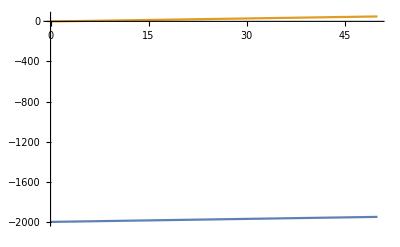

```mathematica
Plot[{p0[r],(r-1)},{r,0,50}]
```

```mathematica
4π (32.4321807293958 .5292 Å)^2
```

```mathematica
H0=ℏ ω0{{1, 0}, {0, 0}};H1=ℏ ωr{{0, Cos[ω t]}, {Cos[ω t], 0}};
```

```mathematica
H1I=MatrixExp[-ⅈ H0 t/ℏ].H1.MatrixExp[-ⅈ H0 t/ℏ]//Simplify
```

{{0,ⅇ^(-ⅈ t ω0) ωr ℏ Cos[t ω]},{ⅇ^(-ⅈ t ω0) ωr ℏ Cos[t ω],0}}

```mathematica
UIt=ⅈ/ℏ Integrate[H1I,{t,0,t1}]//Simplify
```

{{0,(ⅇ^(-ⅈ t1 ω0) ωr (ⅇ^(ⅈ t1 ω0) ω0-ω0 Cos[t1 ω]-ⅈ ω Sin[t1 ω]))/(-ω^2+ω0^2)},{(ⅇ^(-ⅈ t1 ω0) ωr (ⅇ^(ⅈ t1 ω0) ω0-ω0 Cos[t1 ω]-ⅈ ω Sin[t1 ω]))/(-ω^2+ω0^2),0}}

```mathematica
ψt1=UIt.{0,1}
```

{(ⅇ^(-ⅈ t1 ω0) ωr (ⅇ^(ⅈ t1 ω0) ω0-ω0 Cos[t1 ω]-ⅈ ω Sin[t1 ω]))/(-ω^2+ω0^2),0}

```mathematica
ψt1 .H1.ψt1
```

{{0}}